## Real spherical harmonics Y_lm

```mathematica
ClearAll["Global`*"]
```

Define a custom style for outputting data

```mathematica
style[object_,xcolor_]:=Style[object,xcolor,19,FontFamily->"Times",Bold];
```

Transform from degrees into radians

```mathematica
rad[x_]:=x*π/180;
```

### Creating the standard expressions for the spherical harmonics for a given orbital quantum number l

```mathematica
YLM[l_,m_]:=SphericalHarmonicY[l,m,θ,φ];
harmonicSet[l_]:=Table[YLM[l,k],{k,-l,l,1}];
(*create the expressionf for Y_(20,2-2,02,)*)
q2HarmonicSet=Table[{StringTemplate["Y_2.(θ , φ) = "][k],YLM[2,k]},{k,-2,2,2}];
```

Standard expressions Y_lm(θ,φ)

```mathematica
Do[Print[style[q2HarmonicSet[[i]][[1]],Red],"",style[q2HarmonicSet[[i]][[2]],Blue]],{i,1,Length[q2HarmonicSet]}]
```

Y_(2-2)(θ , φ) = 1/4 ⅇ^(-2 ⅈ φ) √(15/(2 π)) Sin[θ]^2

Y_20(θ , φ) = 1/4 √(5/π) (-1+3 Cos[θ]^2)

Y_22(θ , φ) = 1/4 ⅇ^(2 ⅈ φ) √(15/(2 π)) Sin[θ]^2

### Creating the representation of the spherical harmonics in terms of a real basis -Graphics-

```mathematica
YLMRealBasis[l_,m_]:={Sqrt[2]*(-1)^m Im[YLM[l,Abs[m]]],YLM[l,0],Sqrt[2]*(-1)^m Re[YLM[l,m]]};
YLMComplexBasis[l_,m_]:={1/Sqrt[2](YLM[l,Abs[m]]-I*YLM[l,-Abs[m]]),YLM[l,0],(-1)^m/Sqrt[2](YLM[l,Abs[m]]+I*YLM[l,-Abs[m]])};
RealYLM[l_,m_]:=If[m<0,YLMRealBasis[l,m][[1]],If[m>0,YLMRealBasis[l,m][[3]],YLMRealBasis[l,m][[2]]]];
ComplexYLM[l_,m_]:=If[m<0,YLMComplexBasis[l,m][[1]],If[m>0,YLMComplexBasis[l,m][[3]],YLMComplexBasis[l,m][[2]]]];
```

```mathematica
Do[Print[style[StringTemplate["Y_2.^Real = "][k],Black],style[RealYLM[2,k],Black],style[StringTemplate["\n  Y_2.^Im = "][k],Red],style[ComplexYLM[2,k],Red]],{k,-2,2,2}]
```

Y_(2-2)^Real = 1/4 √(15/π) Im[ⅇ^(2 ⅈ φ) Sin[θ]^2]
  Y_(2-2)^Im = (-1/4 ⅈ ⅇ^(-2 ⅈ φ) √(15/(2 π)) Sin[θ]^2+1/4 ⅇ^(2 ⅈ φ) √(15/(2 π)) Sin[θ]^2)/(√2)

Y_20^Real = 1/4 √(5/π) (-1+3 Cos[θ]^2)
  Y_20^Im = 1/4 √(5/π) (-1+3 Cos[θ]^2)

Y_22^Real = 1/4 √(15/π) Re[ⅇ^(2 ⅈ φ) Sin[θ]^2]
  Y_22^Im = (1/4 ⅈ ⅇ^(-2 ⅈ φ) √(15/(2 π)) Sin[θ]^2+1/4 ⅇ^(2 ⅈ φ) √(15/(2 π)) Sin[θ]^2)/(√2)

### Create a graphical representation for a function expressed in terms of Spherical Harmonics (real basis for the spherical functions)

```mathematica
(*Test parameters for the V-function*)
f=2;
g=2;
thetaMin=rad[90];
phiMin=rad[180];
VFunction[f_,g_]:=f*RealYLM[2,0]+g(RealYLM[2,2]+RealYLM[2,-2]);
```

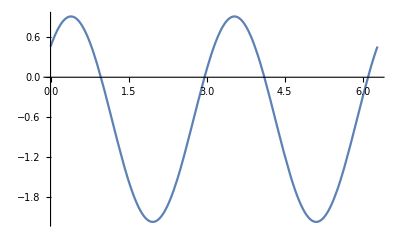

```mathematica
Plot[VFunction[f,g]/.{θ->thetaMin},{φ,0,2π}]
```

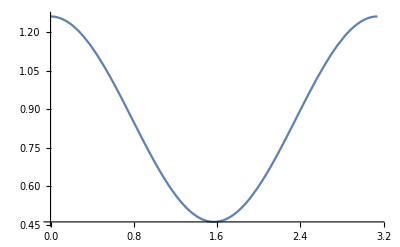

```mathematica
Plot[VFunction[f,g]/.{φ->phiMin},{θ,0,π}]
```